# 球面艺术

```mathematica
s={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
ParametricPlot3D[s,{u,0,2π},{v,0,π}]
```

-Graphics3D-

-Graphics3D-

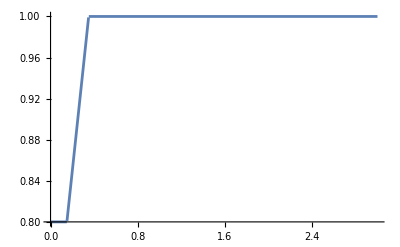

```mathematica
Plot[Clip[x+0.65,{0.8,1}],{x,0,3}]
```

```mathematica
pts=SpherePoints[10];
f[p_]:=Min[Norm[p-#]&/@pts]
ParametricPlot3D[s Clip[f@s+0.65,{0.8,1}],{u,0,2π},{v,0,π}]
```

-Graphics3D-

### 光滑函数

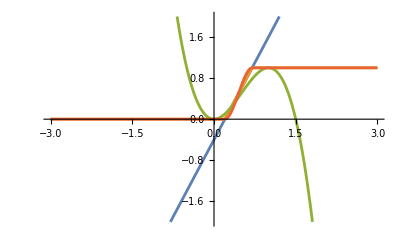

```mathematica
a=(x-0.2)/(0.7-0.2);
b=Clip[a,{0,1}];
c=-2 x^3+3 x^2;

d=c/.{x->b};
Plot[{a,b,c,d},{x,-3,3},PlotRange->2]
```

-2 x^3+3 x^2
这是一个三次函数，且经过原点和{1，1}点

定义SmoothStep函数

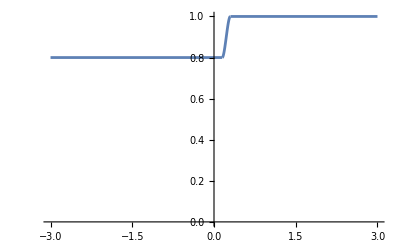

```mathematica
smoothStep[a_,b_,x_]:=-2 t^3+3 t^2/.{t->Clip[(x-a)/(b-a),{0,1}]}
Plot[smoothStep[0.15,0.3,x]0.2+0.8,{x,-3,3},PlotRange->{0,1}]
```

```mathematica
f[p_]:=Min[Norm[p-#]&/@pts]
r=smoothStep[0.15,0.3,f@s]0.15+0.85;
ParametricPlot3D[s r,{u,0,2π},{v,0,π},PlotPoints->50,Mesh->None]
```

-Graphics3D-

### 最终代码

```mathematica
pts=SpherePoints[12];f[p_]:=Min[Norm[p-#]&/@pts]
r=smoothStep[0.15,0.33,f@s]0.15+0.85;
ParametricPlot3D[s r,{u,0,2π},{v,0,π},PlotPoints->120,Mesh->None,PlotStyle->MaterialShading["Glazed"]]
```

-Graphics3D-

```mathematica
pts=SpherePoints[12];f[p_]:=Min[Norm[p-#]&/@pts]
r=(smoothStep[0.15,0.33,x]-smoothStep[0.4,0.52,x])0.15+0.85/.{x->f@s};
ParametricPlot3D[s r,{u,0,2π},{v,0,π},PlotPoints->120,Mesh->None,PlotStyle->MaterialShading["Glazed"]]
```

-Graphics3D-

```mathematica
pts=SpherePoints[12];f[p_]:=Min[Norm[p-#]&/@pts]
r=(smoothStep[0.12,0.3,x]-smoothStep[0.3,0.5,x])0.15+0.85/.{x->f@s};
ParametricPlot3D[s r,{u,0,2π},{v,0,π},PlotPoints->120,Mesh->None,PlotStyle->MaterialShading["Glazed"]]
```

-Graphics3D-